barrier potential

```mathematica
u[x_]:=d ⅇ^(-(-1/2+x)^2/(2 s^2))-(ⅇ^(-(-1-b+x)^2/(2 a^2))+ⅇ^(-(b+x)^2/(2 a^2))) k+1/2 w (2+Erf[r (-1-m+x)]-Erf[r (m+x)])
```

```mathematica
params= {k->2.530,w->50,a->0.03371,b->0.004491,s->0.3,sigma0->0.02,r->21.428,d->2.0,m->0.1078};
(* for lambda particle *)
```

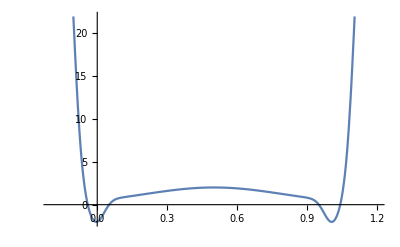

```mathematica
Plot[u[x]/.params,{x,-0.2,1.2}]
```

```mathematica
params1= {k->2.530,w->50,a->0.03371,b->0.004491,s->0.3,sigma0->0.02,r->21.428,d->0.0,m->0.1078}; (* for buffer particle *)
```

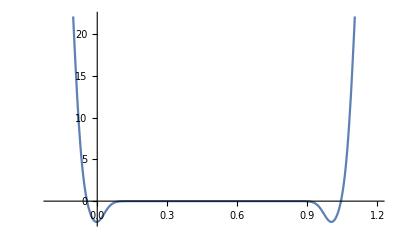

```mathematica
Plot[u[x]/.params1,{x,-0.2,1.2}]
```

derivative of the potential

```mathematica
g[x_]:=1/2 ((2 ⅇ^(-r^2 (-1-m+x)^2) r)/(√π)-(2 ⅇ^(-r^2 (m+x)^2) r)/(√π)) w-(d ⅇ^(-(-1/2+x)^2/(2 s^2)) (-1/2+x))/s^2-k (-(ⅇ^(-(-1-b+x)^2/(2 a^2)) (-1-b+x))/a^2-(ⅇ^(-(b+x)^2/(2 a^2)) (b+x))/a^2)
```

leap frog integrator

```mathematica
leapFrog[x_,v_,p_,step_]:=Module[{x1,v1},
v1=v+dt*(-g[x]/.p)/mass;
v1=andersen[step,v1]; (* temperature coupling *)
x1=x+dt*v1;
Return[{x1,v1}];
]
```

andersen thermostat

```mathematica
andersen[step_,v_]:=Module[{},
If[Mod[step,tau] == 0,
Return[RandomVariate[NormalDistribution[0,0.5],1][[1]]],
Return[v]];
];
```

initial parameters

```mathematica
(*integration parameters*)
nsteps=1000000;
dt=0.001;
tau=200;
(*initial conditions*)
vold=RandomVariate[NormalDistribution[0,0.5],1][[1]];
xold=0;
mass=10;
tol=10^-10;
constr=1;
(*trajectory*)
pos=ConstantArray[0,nsteps];
posb=ConstantArray[0,nsteps];
vel=ConstantArray[0,nsteps];
velb=ConstantArray[0,nsteps];
pos[[1]]=xold;
vel[[1]]=vold;
posb[[1]]=constr-pos[[1]];
velb[[1]]-vold;
(*MD*)
For[t=2,t<=nsteps,t++,
{
(*md step*)
{pos[[t]],vel[[t]]}=leapFrog[pos[[t-1]],vel[[t-1]],params,t];
{posb[[t]],velb[[t]]}=leapFrog[posb[[t-1]],velb[[t-1]],params1,t];
};
];
```

```mathematica
ListPlot[{pos,posC}]
```

-Graphics-

```mathematica
ListPlot[vel+velb]
```

-Graphics-

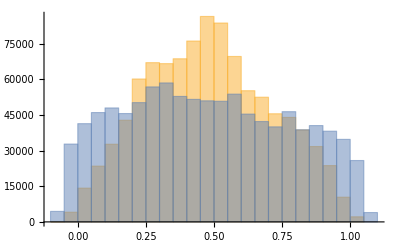

```mathematica
Histogram[{posb,posbC}]
```

constraints SHAKE

```mathematica
updatePosSHAKE[x1_,x2_,const_,tol_]:=Module[{x1O,x2O,x1N,x2N},
x1O=x1;
x2O=x2;
While[Abs[x1O+x2O-const]>tol,
x1N=x1O-(x1O+x2O-const)*0.5;
x2N=x2O-(x1O+x2O-const)*0.5;
x1O=x1N;
x2O=x2N;
];
Return[{x1O,x2O}];
]
```

```mathematica
leapFrogC[x1_,v1_,p1_,x2_,v2_,p2_,step_]:=Module[{x1n,v1n,x2n,v2n},
v1n=v1+dt*(-g[x1]/.p1)/mass;
v2n=v2+dt*(-g[x2]/.p2)/mass;
v1n=andersen[step,v1n]; (* temperature coupling *)
 v2n=If[Mod[step,tau] == 0,-v1n,v2n];
x1n=x1+dt*v1n;
x2n=x2+dt*v2n;
Return[{x1n,v1n,x2n,v2n}];
]
```

```mathematica
(*integration parameters*)
nsteps=1000000;
dt=0.001;
tau=200;
(*initial conditions*)
vold=RandomVariate[NormalDistribution[0,0.5],1][[1]];
xold=0;
mass=10;
tol=10^-10;
constr=1;
(*trajectory*)
posC=ConstantArray[0,nsteps];
posbC=ConstantArray[0,nsteps];
velC=ConstantArray[0,nsteps];
velbC=ConstantArray[0,nsteps];
posC[[1]]=xold;
velC[[1]]=vold;
posbC[[1]]=constr-posC[[1]];
velbC[[1]]-vold;
(*MD*)
For[t=2,t<=nsteps,t++,
{
(*md step*)
{posC[[t]],velC[[t]],posbC[[t]],velbC[[t]]}=
leapFrogC[
posC[[t-1]],velC[[t-1]],params,
posbC[[t-1]],velbC[[t-1]],params1,
t
];
(*constraints*)
{pos[[t]],posb[[t]]}=updatePosSHAKE[pos[[t]],posb[[t]],constr,tol];
(*velocity reconstruction*)
vel[[t]]=(pos[[t]]-pos[[t-1]])/dt;
velb[[t]]=(posb[[t]]-posb[[t-1]])/dt;
If[Mod[t,10000]==0,a=pos[[t]]+posb[[t]]];
};
];
```

```mathematica
Dynamic[t]
```

```mathematica
Dynamic[a]
```

```mathematica
xold
```

999.023

```mathematica
vold|
```

99.9023